Sorting Algorithm Analysis

## Introduction

Problem Description

n elements set : A = {a_1,a_2,...,a_k,... a_(n-1),a_n}

n! elements full distinct sequence set on A: S = {s ∈ {Permute A }};

k-order flag function on sequence s=a_1 a_2...,a_k... a_(n-1),a_n:
	flag[s,k] := i_1 i_2... i_(n-k); {i_m=Piecewise[{{1, a_m<=a_(m+1)}, {0, a_m>a_(m+1)}}], 1 ≤ k ≤ n-1 }
k-Order set on S: F^k = { F^k = flag[s,k] }
define 1^k=1_1 1_2... 1_(n-k); 0^k=0_1 0_2... 0_(n-k)

Sorting any sequence s=a_1 a_2...,a_k... a_(n-1),a_n with an Algorithm M is is equal to find a 
path from {F^(n-1)F^(n-2)... F^2 F^1} to {1^(n-1)1^(n-2)... 1^2 1^1}
M[s=a_1 a_2...,a_k... a_(n-1),a_n]= Ordered[s] equals to 
M[F^(n-1)F^(n-2)... F^2 F^1]to [1^(n-1)1^(n-2)... 1^2 1^1]

Sign_(n-dimention)^(k-order)[0|1] Space Description

k-order flag function flag[s,k]
1 to k order path: f^1→f^2→ ...→ f^(k-1)→ f^k:
sorting problem transfered to n-dimention [1|0]space walking problem
Sorting algorithms reflects the means of walking from original sequence to 
 1^(n-1)1^(n-2)... 1^2 1^1

Sign_(n-dimention)^(k-order)[0|1] Space order ascending

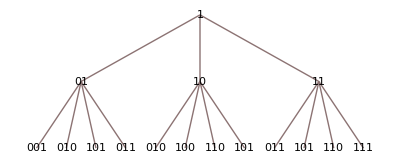
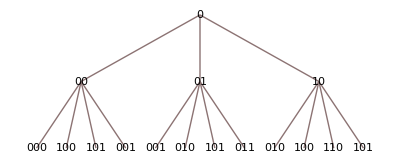

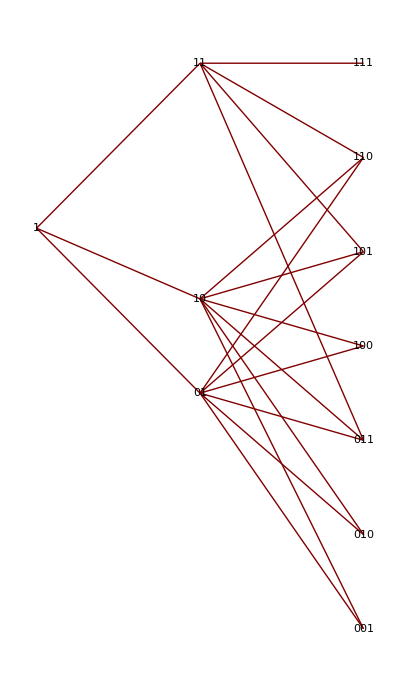
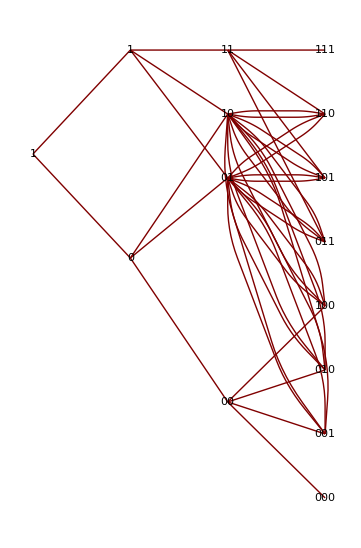

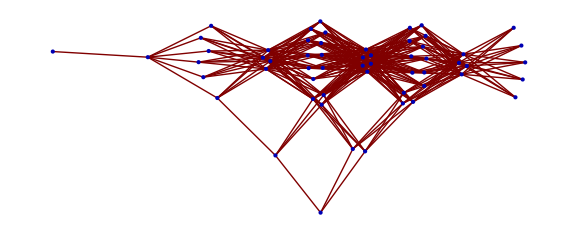

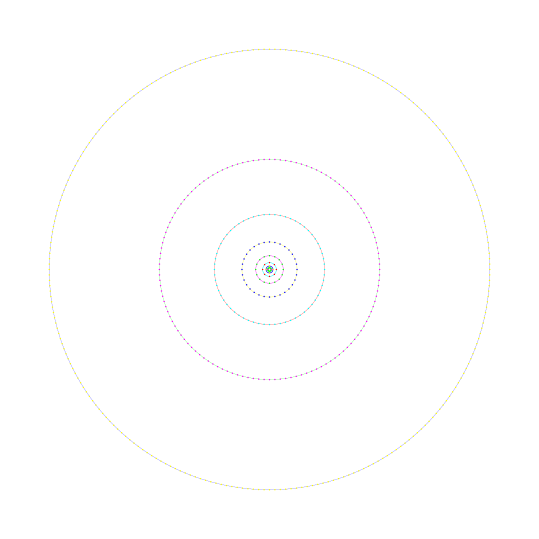

<|"11"→1,"10"→2,"01"→2,"00"→1|>

<|"111"→1,"110"→3,"101"→5,"100"→3,"011"→3,"010"→5,"001"→3,"000"→1|>

<|"1111"→1,"1110"→4,"1101"→9,"1100"→6,"1011"→9,"1010"→16,"1001"→11,"1000"→4,"0111"→4,"0110"→11,"0101"→16,"0100"→9,"0011"→6,"0010"→9,"0001"→4,"0000"→1|>

<|"11111"→1,"11110"→5,"11101"→14,"11100"→10,"11011"→19,"11010"→35,"11001"→26,"11000"→10,"10111"→14,"10110"→40,"10101"→61,"10100"→35,"10011"→26,"10010"→40,"10001"→19,"10000"→5,"01111"→5,"01110"→19,"01101"→40,"01100"→26,"01011"→35,"01010"→61,"01001"→40,"01000"→14,"00111"→10,"00110"→26,"00101"→35,"00100"→19,"00011"→10,"00010"→14,"00001"→5,"00000"→1|>

<|"111111"→1,"111110"→6,"111101"→20,"111100"→15,"111011"→34,"111010"→64,"111001"→50,"111000"→20,"110111"→34,"110110"→99,"110101"→155,"110100"→90,"110011"→71,"110010"→111,"110001"→55,"110000"→15,"101111"→20,"101110"→78,"101101"→169,"101100"→111,"101011"→155,"101010"→272,"101001"→181,"101000"→64,"100111"→50,"100110"→132,"100101"→181,"100100"→99,"100011"→55,"100010"→78,"100001"→29,"100000"→6,"011111"→6,"011110"→29,"011101"→78,"011100"→55,"011011"→99,"011010"→181,"011001"→132,"011000"→50,"010111"→64,"010110"→181,"010101"→272,"010100"→155,"010011"→111,"010010"→169,"010001"→78,"010000"→20,"001111"→15,"001110"→55,"001101"→111,"001100"→71,"001011"→90,"001010"→155,"001001"→99,"001000"→34,"000111"→20,"000110"→50,"000101"→64,"000100"→34,"000011"→15,"000010"→20,"000001"→6,"000000"→1|>

<|"1111111"→1,"1111110"→7,"1111101"→27,"1111100"→21,"1111011"→55,"1111010"→105,"1111001"→85,"1111000"→35,"1110111"→69,"1110110"→203,"1110101"→323,"1110100"→189,"1110011"→155,"1110010"→245,"1110001"→125,"1110000"→35,"1101111"→55,"1101110"→217,"1101101"→477,"1101100"→315,"1101011"→449,"1101010"→791,"1101001"→531,"1101000"→189,"1100111"→155,"1100110"→413,"1100101"→573,"1100100"→315,"1100011"→181,"1100010"→259,"1100001"→99,"1100000"→21,"1011111"→27,"1011110"→133,"1011101"→365,"1011100"→259,"1011011"→477,"1011010"→875,"1011001"→643,"1011000"→245,"1010111"→323,"1010110"→917,"1010101"→1385,"1010100"→791,"1010011"→573,"1010010"→875,"1010001"→407,"1010000"→105,"1001111"→85,"1001110"→315,"1001101"→643,"1001100"→413,"1001011"→531,"1001010"→917,"1001001"→589,"1001000"→203,"1000111"→125,"1000110"→315,"1000101"→407,"1000100"→217,"1000011"→99,"1000010"→133,"1000001"→41,"1000000"→7,"0111111"→7,"0111110"→41,"0111101"→133,"0111100"→99,"0111011"→217,"0111010"→407,"0111001"→315,"0111000"→125,"0110111"→203,"0110110"→589,"0110101"→917,"0110100"→531,"0110011"→413,"0110010"→643,"0110001"→315,"0110000"→85,"0101111"→105,"0101110"→407,"0101101"→875,"0101100"→573,"0101011"→791,"0101010"→1385,"0101001"→917,"0101000"→323,"0100111"→245,"0100110"→643,"0100101"→875,"0100100"→477,"0100011"→259,"0100010"→365,"0100001"→133,"0100000"→27,"0011111"→21,"0011110"→99,"0011101"→259,"0011100"→181,"0011011"→315,"0011010"→573,"0011001"→413,"0011000"→155,"0010111"→189,"0010110"→531,"0010101"→791,"0010100"→449,"0010011"→315,"0010010"→477,"0010001"→217,"0010000"→55,"0001111"→35,"0001110"→125,"0001101"→245,"0001100"→155,"0001011"→189,"0001010"→323,"0001001"→203,"0001000"→69,"0000111"→35,"0000110"→85,"0000101"→105,"0000100"→55,"0000011"→21,"0000010"→27,"0000001"→7,"0000000"→1|>

<|"111111111"→1,"111111110"→9,"111111101"→44,"111111100"→36,"111111011"→119,"111111010"→231,"111111001"→196,"111111000"→84,"111110111"→209,"111110110"→621,"111110101"→1006,"111110100"→594,"111110011"→511,"111110010"→819,"111110001"→434,"111110000"→126,"111101111"→251,"111101110"→999,"111101101"→2224,"111101100"→1476,"111101011"→2149,"111101010"→3801,"111101001"→2576,"111101000"→924,"111100111"→799,"111100110"→2151,"111100101"→3026,"111100100"→1674,"111100011"→1001,"111100010"→1449,"111100001"→574,"111100000"→126,"111011111"→209,"111011110"→1041,"111011101"→2896,"111011100"→2064,"111011011"→3871,"111011010"→7119,"111011001"→5264,"111011000"→2016,"111010111"→2731,"111010110"→7779,"111010101"→11804,"111010100"→6756,"111010011"→4949,"111010010"→7581,"111010001"→3556,"111010000"→924,"111001111"→799,"111001110"→2991,"111001101"→6176,"111001100"→3984,"111001011"→5201,"111001010"→9009,"111001001"→5824,"111001000"→2016,"111000111"→1301,"111000110"→3309,"111000101"→4324,"111000100"→2316,"111000011"→1099,"111000010"→1491,"111000001"→476,"111000000"→84,"110111111"→119,"110111110"→711,"110111101"→2356,"110111100"→1764,"110111011"→3961,"110111010"→7449,"110111001"→5804,"110111000"→2316,"110110111"→3871,"110110110"→11259,"110110101"→17594,"110110100"→10206,"110110011"→8009,"110110010"→12501,"110110001"→6166,"110110000"→1674,"110101111"→2149,"110101110"→8361,"110101101"→18056,"110101100"→11844,"110101011"→16451,"110101010"→28839,"110101001"→19144,"110101000"→6756,"110100111"→5201,"110100110"→13689,"110100101"→18694,"110100100"→10206,"110100011"→5599,"110100010"→7911,"110100001"→2906,"110100000"→594,"110011111"→511,"110011110"→2439,"110011101"→6464,"110011100"→4536,"110011011"→8009,"110011010"→14601,"110011001"→10576,"110011000"→3984,"110010111"→4949,"110010110"→13941,"110010101"→20836,"110010100"→11844,"110010011"→8371,"110010010"→12699,"110010001"→5804,"110010000"→1476,"110001111"→1001,"110001110"→3609,"110001101"→7144,"110001100"→4536,"110001011"→5599,"110001010"→9591,"110001001"→6056,"110001000"→2064,"110000111"→1099,"110000110"→2691,"110000101"→3356,"110000100"→1764,"110000011"→701,"110000010"→909,"110000001"→244,"110000000"→36,"101111111"→44,"101111110"→306,"101111101"→1171,"101111100"→909,"101111011"→2356,"101111010"→4494,"101111001"→3629,"101111000"→1491,"101110111"→2896,"101110110"→8514,"101110101"→13529,"101110100"→7911,"101110011"→6464,"101110010"→10206,"101110001"→5191,"101110000"→1449,"101101111"→2224,"101101110"→8766,"101101101"→19241,"101101100"→12699,"101101011"→18056,"101101010"→31794,"101101001"→21319,"101101000"→7581,"101100111"→6176,"101100110"→16434,"101100101"→22759,"101100100"→12501,"101100011"→7144,"101100010"→10206,"101100001"→3881,"101100000"→819,"101011111"→1006,"101011110"→4944,"101011101"→13529,"101011100"→9591,"101011011"→17594,"101011010"→32256,"101011001"→23671,"101011000"→9009,"101010111"→11804,"101010110"→33486,"101010101"→50521,"101010100"→28839,"101010011"→20836,"101010010"→31794,"101010001"→14759,"101010000"→3801,"101001111"→3026,"101001110"→11184,"101001101"→22759,"101001100"→14601,"101001011"→18694,"101001010"→32256,"101001001"→20681,"101001000"→7119,"101000111"→4324,"101000110"→10866,"101000101"→13991,"101000100"→7449,"101000011"→3356,"101000010"→4494,"101000001"→1369,"101000000"→231,"100111111"→196,"100111110"→1134,"100111101"→3629,"100111100"→2691,"100111011"→5804,"100111010"→10866,"100111001"→8371,"100111000"→3309,"100110111"→5264,"100110110"→15246,"100110101"→23671,"100110100"→13689,"100110011"→10576,"100110010"→16434,"100110001"→8009,"100110000"→2151,"100101111"→2576,"100101110"→9954,"100101101"→21319,"100101100"→13941,"100101011"→19144,"100101010"→33486,"100101001"→22121,"100101000"→7779,"100100111"→5824,"100100110"→15246,"100100101"→20681,"100100100"→11259,"100100011"→6056,"100100010"→8514,"100100001"→3079,"100100000"→621,"100011111"→434,"100011110"→2016,"100011101"→5191,"100011100"→3609,"100011011"→6166,"100011010"→11184,"100011001"→8009,"100011000"→2991,"100010111"→3556,"100010110"→9954,"100010101"→14759,"100010100"→8361,"100010011"→5804,"100010010"→8766,"100010001"→3961,"100010000"→999,"100001111"→574,"100001110"→2016,"100001101"→3881,"100001100"→2439,"100001011"→2906,"100001010"→4944,"100001001"→3079,"100001000"→1041,"100000111"→476,"100000110"→1134,"100000101"→1369,"100000100"→711,"100000011"→244,"100000010"→306,"100000001"→71,"100000000"→9,"011111111"→9,"011111110"→71,"011111101"→306,"011111100"→244,"011111011"→711,"011111010"→1369,"011111001"→1134,"011111000"→476,"011110111"→1041,"011110110"→3079,"011110101"→4944,"011110100"→2906,"011110011"→2439,"011110010"→3881,"011110001"→2016,"011110000"→574,"011101111"→999,"011101110"→3961,"011101101"→8766,"011101100"→5804,"011101011"→8361,"011101010"→14759,"011101001"→9954,"011101000"→3556,"011100111"→2991,"011100110"→8009,"011100101"→11184,"011100100"→6166,"011100011"→3609,"011100010"→5191,"011100001"→2016,"011100000"→434,"011011111"→621,"011011110"→3079,"011011101"→8514,"011011100"→6056,"011011011"→11259,"011011010"→20681,"011011001"→15246,"011011000"→5824,"011010111"→7779,"011010110"→22121,"011010101"→33486,"011010100"→19144,"011010011"→13941,"011010010"→21319,"011010001"→9954,"011010000"→2576,"011001111"→2151,"011001110"→8009,"011001101"→16434,"011001100"→10576,"011001011"→13689,"011001010"→23671,"011001001"→15246,"011001000"→5264,"011000111"→3309,"011000110"→8371,"011000101"→10866,"011000100"→5804,"011000011"→2691,"011000010"→3629,"011000001"→1134,"011000000"→196,"010111111"→231,"010111110"→1369,"010111101"→4494,"010111100"→3356,"010111011"→7449,"010111010"→13991,"010111001"→10866,"010111000"→4324,"010110111"→7119,"010110110"→20681,"010110101"→32256,"010110100"→18694,"010110011"→14601,"010110010"→22759,"010110001"→11184,"010110000"→3026,"010101111"→3801,"010101110"→14759,"010101101"→31794,"010101100"→20836,"010101011"→28839,"010101010"→50521,"010101001"→33486,"010101000"→11804,"010100111"→9009,"010100110"→23671,"010100101"→32256,"010100100"→17594,"010100011"→9591,"010100010"→13529,"010100001"→4944,"010100000"→1006,"010011111"→819,"010011110"→3881,"010011101"→10206,"010011100"→7144,"010011011"→12501,"010011010"→22759,"010011001"→16434,"010011000"→6176,"010010111"→7581,"010010110"→21319,"010010101"→31794,"010010100"→18056,"010010011"→12699,"010010010"→19241,"010010001"→8766,"010010000"→2224,"010001111"→1449,"010001110"→5191,"010001101"→10206,"010001100"→6464,"010001011"→7911,"010001010"→13529,"010001001"→8514,"010001000"→2896,"010000111"→1491,"010000110"→3629,"010000101"→4494,"010000100"→2356,"010000011"→909,"010000010"→1171,"010000001"→306,"010000000"→44,"001111111"→36,"001111110"→244,"001111101"→909,"001111100"→701,"001111011"→1764,"001111010"→3356,"001111001"→2691,"001111000"→1099,"001110111"→2064,"001110110"→6056,"001110101"→9591,"001110100"→5599,"001110011"→4536,"001110010"→7144,"001110001"→3609,"001110000"→1001,"001101111"→1476,"001101110"→5804,"001101101"→12699,"001101100"→8371,"001101011"→11844,"001101010"→20836,"001101001"→13941,"001101000"→4949,"001100111"→3984,"001100110"→10576,"001100101"→14601,"001100100"→8009,"001100011"→4536,"001100010"→6464,"001100001"→2439,"001100000"→511,"001011111"→594,"001011110"→2906,"001011101"→7911,"001011100"→5599,"001011011"→10206,"001011010"→18694,"001011001"→13689,"001011000"→5201,"001010111"→6756,"001010110"→19144,"001010101"→28839,"001010100"→16451,"001010011"→11844,"001010010"→18056,"001010001"→8361,"001010000"→2149,"001001111"→1674,"001001110"→6166,"001001101"→12501,"001001100"→8009,"001001011"→10206,"001001010"→17594,"001001001"→11259,"001001000"→3871,"001000111"→2316,"001000110"→5804,"001000101"→7449,"001000100"→3961,"001000011"→1764,"001000010"→2356,"001000001"→711,"001000000"→119,"000111111"→84,"000111110"→476,"000111101"→1491,"000111100"→1099,"000111011"→2316,"000111010"→4324,"000111001"→3309,"000111000"→1301,"000110111"→2016,"000110110"→5824,"000110101"→9009,"000110100"→5201,"000110011"→3984,"000110010"→6176,"000110001"→2991,"000110000"→799,"000101111"→924,"000101110"→3556,"000101101"→7581,"000101100"→4949,"000101011"→6756,"000101010"→11804,"000101001"→7779,"000101000"→2731,"000100111"→2016,"000100110"→5264,"000100101"→7119,"000100100"→3871,"000100011"→2064,"000100010"→2896,"000100001"→1041,"000100000"→209,"000011111"→126,"000011110"→574,"000011101"→1449,"000011100"→1001,"000011011"→1674,"000011010"→3026,"000011001"→2151,"000011000"→799,"000010111"→924,"000010110"→2576,"000010101"→3801,"000010100"→2149,"000010011"→1476,"000010010"→2224,"000010001"→999,"000010000"→251,"000001111"→126,"000001110"→434,"000001101"→819,"000001100"→511,"000001011"→594,"000001010"→1006,"000001001"→621,"000001000"→209,"000000111"→84,"000000110"→196,"000000101"→231,"000000100"→119,"000000011"→36,"000000010"→44,"000000001"→9,"000000000"→1|>

<|"11"→1,"10"→2,"01"→2,"00"→1|>

## Data Import:

```mathematica
dir = Select[FileNames["*",SetDirectory[NotebookDirectory[]],Infinity],DirectoryQ];
Map[(AppendTo[$Path, #1])&,Select[dir, !StringMatchQ[#,RegularExpression[".*\\..*"]]&]];
Directory[]
```

C:\Users\hpzju\Desktop\MyKB\src\MyBooks\Sorting Problem Analysis

```mathematica
Needs["SPAUtilities`"];
```

```mathematica
range = 1000000000000;
data1K = RandomInteger[range,10^3];
data10K = RandomInteger[range,10^4];
data100K = RandomInteger[range,10^5];
```

```mathematica
data1M = RandomInteger[range,10^6];
data10M = RandomInteger[range,10^7];
data100M = RandomInteger[range,10^8];
(*data1B = RandomInteger[range,10^9];*)
```

```mathematica
{Timing[l11=Sort[data1K];l12=Sort[RandomInteger[range,10^3]];],
Timing[recursiveMerge[l11,l12];],
Timing[l21=Sort[data10K];l22=Sort[RandomInteger[range,10^4]];],
Timing[recursiveMerge[l12,l22];],
Timing[l31=Sort[data100K];l32=Sort[RandomInteger[range,10^5]];],
Timing[recursiveMerge[l31,l32];],
Timing[l41=Sort[data1M];l42=Sort[RandomInteger[range,10^6]];],
Timing[recursiveMerge[l41,l42];],
Timing[l51=Sort[data10M];l52=Sort[RandomInteger[range,10^7]];],
Timing[recursiveMerge[l51,l52];]
}
```

{{0.,Null},{0.0625,Null},{0.,Null},{0.078125,Null},{0.015625,Null},{4.28125,Null},{0.265625,Null},{43.5625,Null},{2.20313,Null},{62.1875,Null}}

```mathematica
Timing[l61=Sort[data10M];l62=Sort[RandomInteger[range,10^7]];]
```

{3.95313,Null}

```mathematica
Timing[recursiveMerge[l61,l41];]
```

{71.0313,Null}

{{0.,Null},{0.,Null},{0.,Null},{0.,Null},{0.015625,Null},{0.015625,Null},{0.140625,Null},{0.125,Null},{1.9375,Null},{1.25,Null}}

```mathematica
{Timing[h11=hybridSort[data1K];],
Timing[h12=hybridSort[data10K];],
Timing[h13=hybridSort[data100K];]}
```

{{0.,Null},{0.,Null},{0.03125,Null}}

```mathematica
h13==l13
```

False

```mathematica
l13[[1;;10]]
```

{4206288,5798267,10343231,11541907,15017221,16990637,18105495,19880045,25199735,41384310}

```mathematica
l=l13[[1;;10]]
```

{4206288,5798267,10343231,11541907,15017221,16990637,18105495,19880045,25199735,41384310}

```mathematica
recursiveMerge[l,l]
```

in

{4206288,5798267,10343231,11541907,15017221,16990637,18105495,19880045,25199735,41384310,4206288,5798267,10343231,11541907,15017221,16990637,18105495,19880045,25199735,41384310}

```mathematica
Dimensions[h13]
```

{100000}

```mathematica
{Timing[h11=hybridSort[data1K];],
Timing[h12=hybridSort[data10K];],
Timing[h13=hybridSort[data100K];],
Timing[h14=hybridSort[data1M];],
Timing[h15=hybridSort[data10M];]}
```

$Aborted

```mathematica
{Timing[l16=hybridSort[data100M];],Timing[h16=hybridSort[data100M];]}
```

{{0.,Null},{0.,Null},{0.03125,Null},{0.1875,Null},{3.21875,Null},{36.3281,Null}}

```mathematica
data1B = RandomInteger[range,10^9];
```

```mathematica
Timing[Sort[data1B];]
```

```mathematica
Timing[h16=hybridSort[data1B];]
```

{42.0469,Null}

```mathematica
ByteCount[data1M]
```

8000144

```mathematica
{l11==Flatten[h11], l12==Flatten[h12],l13==Flatten[h13],l14==Flatten[h14],l15==Flatten[h15],l16==Flatten[h16]}
```

{True,True,True,True,True,True}

## Testing:

```mathematica
l1={2,4,9,10,11,12,12,89,199,199};
For[i=1,i<=Length[l1],i++,
	If[ !stableFind[l1,i] == i+1, Print[i,": ",stableFind[l1,i]], Print[i,": ok"]]];
```

```mathematica
l1={2,4,9,10,11,12,12,89,199,199};
For[i=1,i<=Length[l1],i++,
	If[ !stableInsert[l1,l1[[i]]] == i+1, Print[i,": ",stableInsert[l1,l1[[i]]]], Print[i,": ok"]]];
```

```mathematica
l1={2,4,9,10,11,12,12,89,199,199};
For[i=1,i<=Length[l1],i++,
	If[ !unStableFind[l1,i] == i, Print[i,": ",unStableFind[l1,i]], Print[i,": ok"]]];
```

```mathematica
l1={2,4,9,10,11,12,12,89,199,199};
For[i=1,i<=Length[l1],i++,
	If[ !unStableInsert[l1,l1[[i]]] == i, Print[i,": ",unStableInsert[l1,l1[[i]]]], Print[i,": ok"]]];
```

```mathematica
{stableInsert[l1,0],stableInsert[l1,200], unStableInsert[l1,0],unStableInsert[l1,200]}
```

```mathematica
{stableInsert[l1,2],stableInsert[l1,199], unStableInsert[l1,2],unStableInsert[l1,199]}
```

{2,11,1,9}

```mathematica
a=RandomInteger[100,20]; b = RandomInteger[100,100];
Sort[{a,b}]== recursiveMerge[a,b]
```

```mathematica
a=Sort[RandomInteger[100,489985]]; b = Sort[RandomInteger[100,388834]];
Sort[Join[a,b]]== recursiveMerge[a,b]
```

True

```mathematica
a={2,3,8,90}; b ={0,4,8,109};
Sort[Join[a,b]]== recursiveMerge[a,b]
```

{ma, mb}={2,2}

F:{posa, posb}={3,2}

True

```mathematica
recursiveMerge[a,b]
```

{ma, mb}={2,2}

T:{posa, posb}={1,4}

{7,8,30,49,88,89}

```mathematica
Sort[Join[a,b]]
```

{7,8,30,49,88,89}

```mathematica
a
```

{30,88,89}

```mathematica
b
```

{7,8,49}

```mathematica
Sort[Join[a,b]]
```

{23,29,31,49,60,90}

```mathematica
{a,b}
```

{{53,81,45},{64,97}}

```mathematica
recursiveMerge[a,b]
```

{ma, mb}={2,1}

{45,53,64,81,97}

```mathematica
?c
```

Global`c

c=Null

?

## Coding 5:

Functions:

```mathematica
sampleData[n_]:= RandomSample[Range[n]];
data = sampleData[13];
```

```mathematica
maxOrdered[seq_]:=Module[{matrix={{seq[[1]]}}},
For[i=2,i≤Length[seq],i++,
	For[j=1,j≤Length[matrix],j++,
		If[seq[[i]]<matrix[[j,-1]],
		AppendTo[matrix,{seq[[i]]}],
		AppendTo[matrix[[j]],seq[[i]]]
		];
	];
	];
Return[matrix];
];
```

```mathematica
sequenceCoding[seq_, order_:1]:=Module[{list,str},
list=Thread[Greater[seq[[1;;-(order+1)]],seq[[order+1;;-1]]]] /. {True ->0, False ->1};
str=Apply[StringJoin,Map[ToString,list]];
Return[{list,{str,Counts[list]}}];
];
```

```mathematica
sequenceCoding[data]
```

```mathematica
sequenceCoding[data,4]
```

{{0,0,1,0,0,1,0,0,1},{001001001,<|0→6,1→3|>}}

```mathematica
data
```

{7,12,5,13,4,8,10,9,2,11,1,3,6}

```mathematica
maxOrdered[data]
```

{{7,12,13},{5,5,13},{4,4,8,10,11},{4,4,8,10,11},{8,8,10,11},{8,8,10,11},{10,10,11},{10,10,11},{9,9,11},{9,9,11},{9,9,11},{9,9,11},{9,9,11},{9,9,11},{9,9,11},{9,9,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{2,2,11},{11,11},{11,11},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{1,1,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{3,3,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6},{6,6}}

## Coding 4:

Functions:

```mathematica
plotAllOrders[n_]:=Module[{points, circles, colors},
colors = {Red,Green, Blue, Cyan, Magenta, Yellow}; 
points=Table[{colors[[Mod[i+3,6]+1]],AbsolutePointSize[1],Point[{2^(i-1) Cos[2π/2^i j],2^(i-1) Sin[2π/2^i j]}]},{i,1,n},{j,0,2^i-1}];
circles=Table[{colors[[Mod[i,6]+1]],AbsoluteThickness[1/i],Circle[{0,0},2^(i-1)]},{i,1,n}];
(*Print[points];
Print[circles];*)
g =Graphics[{Flatten[circles],Flatten[points]}];

Show[g]
]
```

```mathematica
plotToNextOrders[n_]:=Module[{points, circles,colors},
colors = {Red,Green}; 
points=Table[{colors[[Mod[i,2]+1]],AbsolutePointSize[2],Point[{2^(i-1) Cos[2π/2^i j],2^(i-1) Sin[2π/2^i j]}]},{i,n,n+1},{j,0,2^i-1}];
circles=Table[{AbsoluteThickness[1/i],Circle[{0,0},2^(i-1)]},{i,n,n+1}];
lines = Table[{AbsoluteThickness[1/i],Circle[{0,0},2^(i-1)]},{i,n,n+1}];
Print[points];
Print[circles];
g =Graphics[{Flatten[circles],Flatten[points]}];

Show[g]
]
```

{{{RGBColor[0, 1, 0],AbsolutePointSize[2],Point[{4,0}]},{RGBColor[0, 1, 0],AbsolutePointSize[2],Point[{2 √2,2 √2}]},{RGBColor[0, 1, 0],AbsolutePointSize[2],Point[{0,4}]},{RGBColor[0, 1, 0],AbsolutePointSize[2],Point[{-2 √2,2 √2}]},{RGBColor[0, 1, 0],AbsolutePointSize[2],Point[{-4,0}]},{RGBColor[0, 1, 0],AbsolutePointSize[2],Point[{-2 √2,-2 √2}]},{RGBColor[0, 1, 0],AbsolutePointSize[2],Point[{0,-4}]},{RGBColor[0, 1, 0],AbsolutePointSize[2],Point[{2 √2,-2 √2}]}},{{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{8,0}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{8 Cos[π/8],8 Sin[π/8]}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{4 √2,4 √2}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{8 Sin[π/8],8 Cos[π/8]}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{0,8}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{-8 Sin[π/8],8 Cos[π/8]}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{-4 √2,4 √2}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{-8 Cos[π/8],8 Sin[π/8]}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{-8,0}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{-8 Cos[π/8],-8 Sin[π/8]}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{-4 √2,-4 √2}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{-8 Sin[π/8],-8 Cos[π/8]}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{0,-8}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{8 Sin[π/8],-8 Cos[π/8]}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{4 √2,-4 √2}]},{RGBColor[1, 0, 0],AbsolutePointSize[2],Point[{8 Cos[π/8],-8 Sin[π/8]}]}}}

{{AbsoluteThickness[1/3],Circle[{0,0},4]},{AbsoluteThickness[1/4],Circle[{0,0},8]}}

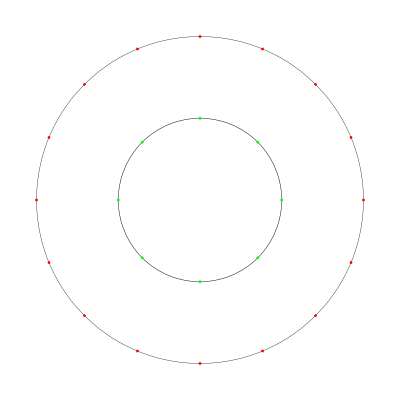

```mathematica
plotToNextOrders[3]
```

```mathematica
plotAllOrders[8]
```

-Graphics-

## Coding 3:

Functions:

```mathematica
generateLeafs[list_]:=Module[{},Union[Permutations[Append[list,"0"]],Permutations[Append[list,"1"]]]];
generateString[list_]:=Module[{},Apply[StringJoin,list,{-2}]];
mappingLeafs[roots_, leafs_]:=Outer[Rule,roots,leafs];
```

```mathematica
tree2 = {"1"-> "01","1"-> "10","1"-> "11"};
seedList2 ={{"0","1"},{"1","0"},{"1","1"}};
stringList2 = {{"01"},{"10"},{"11"}};
```

```mathematica
generateTree[n_]:=Module[{list,seedList=seedList2,strList, prevstrList=stringList2,tmpstrList,tree=tree2,tmptree}, 
For[i=2,i<n,i++,
list = Map[generateLeafs,seedList];
seedList = Flatten[list, 1];
strList = Apply[StringJoin,list,{-2}];
tmpstrList = Thread[List[Flatten[prevstrList,1]]];
tmptree = MapThread[mappingLeafs,{tmpstrList,strList}];
tree = Join[tree, Flatten[tmptree]];
prevstrList = strList;
];
tree]
```

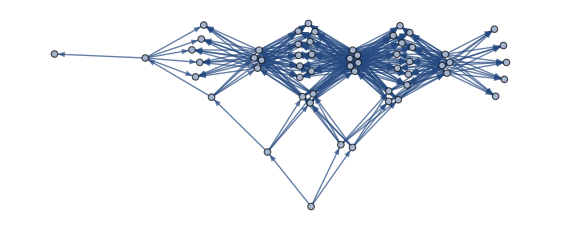

```mathematica
t = generateTree[5];
A = Counts[t];
B=Apply[List,Normal[A],{1}];
d=Flatten[B[[;;,1]]];
w=B[[;;,2]];
g = Graph[d, EdgeWeight->w]
```

```mathematica
w
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,15,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,10,1,1,1,1,1,1}

```mathematica
GraphPlot[d]
```

-Graphics-

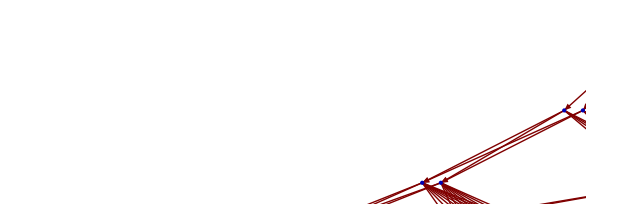

Generate 3 Layer Tree:

```mathematica
list3 = Map[generateLeafs,seedList2];
seedList3 = Flatten[list3, 1];
stringList3 = Apply[StringJoin,list3,{-2}];
tmptree3 = MapThread[mappingLeafs,{stringList2,stringList3}];
tree3 = Join[tree2, Flatten[tmptree3]];
```

```mathematica
TreePlot[tree3,Left,VertexLabeling->True]
```

-Graphics-

Generate 4 Layer Tree:

```mathematica
list4 = Map[generateLeafs,seedList3];
seedList4 = Flatten[list4, 1];
stringList4 = Apply[StringJoin,list4,{-2}];
tmpstringlist = Thread[List[Flatten[stringList3,1]]];
tmptree4 = MapThread[mappingLeafs,{tmpstringlist,stringList4}];
tree4 = Join[tree3, Flatten[tmptree4]];
```

```mathematica
TreePlot[Flatten[tree4],Left,VertexLabeling->True]
```

-Graphics-

```mathematica
seedlist3 = Flatten[list3, 1]
```

{{0,0},{0,1},{1,0},{0,1},{1,0},{1,1}}

```mathematica
seedlist2
```

{{0},{1}}

```mathematica
stringList3 = Apply[StringJoin,list,{-2}]
```

{{00,01,10},{01,10,11}}

```mathematica
mappingLeafs[seedlist2[[1]],stringList3[[1]] ]
```

{{0→00,0→01,0→10}}

```mathematica
tmptree = MapThread[mappingLeafs,{seedlist2,stringList3}]
```

{{{0→00,0→01,0→10}},{{1→01,1→10,1→11}}}

```mathematica
tree3 = Join[tree2, Flatten[tmptree]]
```

{1→0,1→1,0→00,0→01,0→10,1→01,1→10,1→11}

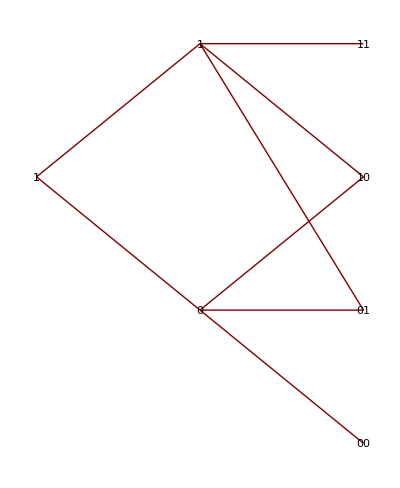

```mathematica
TreePlot[tree3,Left,VertexLabeling->True]
```

```mathematica
Apply[StringJoin,list,{-2}]
```

{{00,01,10},{01,10,11}}

```mathematica
Flatten[list, 1]
```

{{0,0},{0,1},{1,0},{0,1},{1,0},{1,1}}

```mathematica
Join[{2},{4}]
```

{2,4}

```mathematica
Outer[Rule,{1},{"0","1"}]//Flatten
```

{1→0,1→1}

```mathematica
MapThread[Rule,{"1",{"0","1"}]
```

1[0,1]

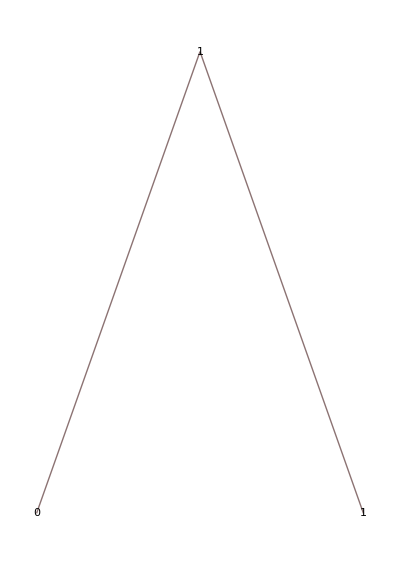

```mathematica
%//TreeForm
```

## Coding 2:

Functions:

```mathematica
generateLeafs[list_]:=Module[{},Union[Permutations[Append[list,"0"]],Permutations[Append[list,"1"]]]];
generateString[list_]:=Module[{},Apply[StringJoin,list,{-2}]];
mappingLeafs[roots_, leafs_]:=Outer[Rule,roots,leafs];
```

Initialize  2 Layer Tree:

```mathematica
tree2 = Flatten[Outer[Rule,{1},{"0","1"}]];
seedList2 ={{"0"},{"1"}};
stringList2 = {{"0"},{"1"}};
```

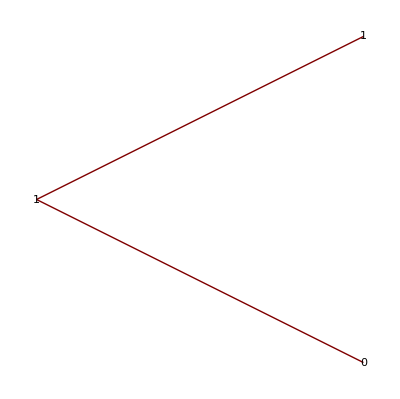

```mathematica
TreePlot[tree2,Left,VertexLabeling->True]
```

Generate 3 Layer Tree:

```mathematica
list3 = Map[generateLeafs,seedlist2];
seedList3 = Flatten[list3, 1];
stringList3 = Apply[StringJoin,list3,{-2}];
tmptree3 = MapThread[mappingLeafs,{stringList2,stringList3}];
tree3 = Join[tree2, Flatten[tmptree3]];
```

```mathematica
TreePlot[tree3,Left,VertexLabeling->True]
```

-Graphics-

Generate 4 Layer Tree:

```mathematica
list4 = Map[generateLeafs,seedList3];
seedList4 = Flatten[list4, 1];
stringList4 = Apply[StringJoin,list4,{-2}];
tmpstringlist = Thread[List[Flatten[stringList3,1]]];
tmptree4 = MapThread[mappingLeafs,{tmpstringlist,stringList4}];
tree4 = Join[tree3, Flatten[tmptree4]];
```

```mathematica
TreePlot[Flatten[tree4],Left,VertexLabeling->True]
```

-Graphics-

```mathematica
seedlist3 = Flatten[list3, 1]
```

{{0,0},{0,1},{1,0},{0,1},{1,0},{1,1}}

```mathematica
seedlist2
```

{{0},{1}}

```mathematica
stringList3 = Apply[StringJoin,list,{-2}]
```

{{00,01,10},{01,10,11}}

```mathematica
mappingLeafs[seedlist2[[1]],stringList3[[1]] ]
```

{{0→00,0→01,0→10}}

```mathematica
tmptree = MapThread[mappingLeafs,{seedlist2,stringList3}]
```

{{{0→00,0→01,0→10}},{{1→01,1→10,1→11}}}

```mathematica
tree3 = Join[tree2, Flatten[tmptree]]
```

{1→0,1→1,0→00,0→01,0→10,1→01,1→10,1→11}

```mathematica
TreePlot[tree3,Left,VertexLabeling->True]
```

-Graphics-

```mathematica
Apply[StringJoin,list,{-2}]
```

{{00,01,10},{01,10,11}}

```mathematica
Flatten[list, 1]
```

{{0,0},{0,1},{1,0},{0,1},{1,0},{1,1}}

```mathematica
Join[{2},{4}]
```

{2,4}

```mathematica
Outer[Rule,{1},{"0","1"}]//Flatten
```

{1→0,1→1}

```mathematica
MapThread[Rule,{"1",{"0","1"}]
```

1[0,1]

```mathematica
%//TreeForm
```

-Graphics-

## Coding 1:

```mathematica
Needs["HPUtilities`"];
```

```mathematica
initPath[NotebookDirectory[]];
```

```mathematica
list = {1,6,2,96,65};
```

```mathematica
Needs["SPAUtilities`"]
```

```mathematica
Head[Less]
```

Symbol

```mathematica
compMatrix[list]
```

{{1,1,1,1,1},{0,1,0,1,1},{0,1,1,1,1},{0,0,0,1,0},{0,0,0,1,1}}

```mathematica
compMatrix[list,Infinity, Less]
```

{{1,0,0,0,0},{1,1,1,0,0},{1,0,1,0,0},{1,1,1,1,1},{1,1,1,0,1}}

```mathematica
compMatrix[list,]
```

compMatrix[{1,6,2,96,65},1,Less&]

```mathematica
sampleData[n_]:=PermutationList[RandomSample[Range[n],n]];
comparisonOrder[list_,k_]:=Module[{tmplist=list[[1;;-(k+1)]]},
ls=Thread[Greater[list[[1;;-(k+1)]],list[[k+1;;-1]]]] /. {True ->0, False ->1};
Apply[StringJoin,Map[ToString,ls]]
];
comparisonOrder1[list_]:=Module[{tmplist=list[[1;;-(1+1)]]},
ls=Thread[Greater[list[[1;;-(1+1)]],list[[1+1;;-1]]]] /. {True ->0, False ->1};
Apply[StringJoin,Map[ToString,ls]]
];
comparisonMatrix[list_]:= Module[{n=Length[list]},
Table[Thread[Greater[Table[list[[i]],n],list]] /. {True ->0, False ->1},{i,n}]
];
plotCompOrders[list_]:=Module[{n = Length[list]},Column[Insert[Table[comparisonOrder[list,k],{k,1,n-1}],list,1],Center]];
plotCompMatrix[list_]:=MatrixForm[comparisonMatrix[list]];
```

```mathematica
permN[n_]:=Permutations[Table[i,{i,n}]];
```

```mathematica
fullOrderN[n_]:=Module[{data = permN[n]},
Print["n=",n];
Print[n,"! = ",n!];
Print["2^",n-1,"=",2^(n-1)];
tmplist=Map[comparisonOrder1,data];
Counts[tmplist]
]
```

```mathematica
plotCompMatrix[{7,12,5,13,4,8,10,9,2,11,1,3,6}]
```

(1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1
0 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0
0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 1
0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 0 | 1 | 0 | 1 | 1
1 | 1 | 0 | 1 | 0 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 1)

```mathematica
fullOrderN[3]
```

n=3

3! = 6

2^2=4

<|11→1,10→2,01→2,00→1|>

```mathematica
fullOrderN[4]
```

n=4

4! = 24

2^3=8

<|111→1,110→3,101→5,100→3,011→3,010→5,001→3,000→1|>

```mathematica
fullOrderN[6]
```

n=6

6! = 720

2^5=32

<|11111→1,11110→5,11101→14,11100→10,11011→19,11010→35,11001→26,11000→10,10111→14,10110→40,10101→61,10100→35,10011→26,10010→40,10001→19,10000→5,01111→5,01110→19,01101→40,01100→26,01011→35,01010→61,01001→40,01000→14,00111→10,00110→26,00101→35,00100→19,00011→10,00010→14,00001→5,00000→1|>

```mathematica
fullOrderN[7]
```

n=7

7! = 5040

2^6=64

<|111111→1,111110→6,111101→20,111100→15,111011→34,111010→64,111001→50,111000→20,110111→34,110110→99,110101→155,110100→90,110011→71,110010→111,110001→55,110000→15,101111→20,101110→78,101101→169,101100→111,101011→155,101010→272,101001→181,101000→64,100111→50,100110→132,100101→181,100100→99,100011→55,100010→78,100001→29,100000→6,011111→6,011110→29,011101→78,011100→55,011011→99,011010→181,011001→132,011000→50,010111→64,010110→181,010101→272,010100→155,010011→111,010010→169,010001→78,010000→20,001111→15,001110→55,001101→111,001100→71,001011→90,001010→155,001001→99,001000→34,000111→20,000110→50,000101→64,000100→34,000011→15,000010→20,000001→6,000000→1|>

```mathematica
fullOrderN[8]
```

n=8

8! = 40320

2^7=128

<|1111111→1,1111110→7,1111101→27,1111100→21,1111011→55,1111010→105,1111001→85,1111000→35,1110111→69,1110110→203,1110101→323,1110100→189,1110011→155,1110010→245,1110001→125,1110000→35,1101111→55,1101110→217,1101101→477,1101100→315,1101011→449,1101010→791,1101001→531,1101000→189,1100111→155,1100110→413,1100101→573,1100100→315,1100011→181,1100010→259,1100001→99,1100000→21,1011111→27,1011110→133,1011101→365,1011100→259,1011011→477,1011010→875,1011001→643,1011000→245,1010111→323,1010110→917,1010101→1385,1010100→791,1010011→573,1010010→875,1010001→407,1010000→105,1001111→85,1001110→315,1001101→643,1001100→413,1001011→531,1001010→917,1001001→589,1001000→203,1000111→125,1000110→315,1000101→407,1000100→217,1000011→99,1000010→133,1000001→41,1000000→7,0111111→7,0111110→41,0111101→133,0111100→99,0111011→217,0111010→407,0111001→315,0111000→125,0110111→203,0110110→589,0110101→917,0110100→531,0110011→413,0110010→643,0110001→315,0110000→85,0101111→105,0101110→407,0101101→875,0101100→573,0101011→791,0101010→1385,0101001→917,0101000→323,0100111→245,0100110→643,0100101→875,0100100→477,0100011→259,0100010→365,0100001→133,0100000→27,0011111→21,0011110→99,0011101→259,0011100→181,0011011→315,0011010→573,0011001→413,0011000→155,0010111→189,0010110→531,0010101→791,0010100→449,0010011→315,0010010→477,0010001→217,0010000→55,0001111→35,0001110→125,0001101→245,0001100→155,0001011→189,0001010→323,0001001→203,0001000→69,0000111→35,0000110→85,0000101→105,0000100→55,0000011→21,0000010→27,0000001→7,0000000→1|>

```mathematica
fullOrderN[10]
```

n=10

10! = 3628800

2^9=512

<|111111111→1,111111110→9,111111101→44,111111100→36,111111011→119,111111010→231,111111001→196,111111000→84,111110111→209,111110110→621,111110101→1006,111110100→594,111110011→511,111110010→819,111110001→434,111110000→126,111101111→251,111101110→999,111101101→2224,111101100→1476,111101011→2149,111101010→3801,111101001→2576,111101000→924,111100111→799,111100110→2151,111100101→3026,111100100→1674,111100011→1001,111100010→1449,111100001→574,111100000→126,111011111→209,111011110→1041,111011101→2896,111011100→2064,111011011→3871,111011010→7119,111011001→5264,111011000→2016,111010111→2731,111010110→7779,111010101→11804,111010100→6756,111010011→4949,111010010→7581,111010001→3556,111010000→924,111001111→799,111001110→2991,111001101→6176,111001100→3984,111001011→5201,111001010→9009,111001001→5824,111001000→2016,111000111→1301,111000110→3309,111000101→4324,111000100→2316,111000011→1099,111000010→1491,111000001→476,111000000→84,110111111→119,110111110→711,110111101→2356,110111100→1764,110111011→3961,110111010→7449,110111001→5804,110111000→2316,110110111→3871,110110110→11259,110110101→17594,110110100→10206,110110011→8009,110110010→12501,110110001→6166,110110000→1674,110101111→2149,110101110→8361,110101101→18056,110101100→11844,110101011→16451,110101010→28839,110101001→19144,110101000→6756,110100111→5201,110100110→13689,110100101→18694,110100100→10206,110100011→5599,110100010→7911,110100001→2906,110100000→594,110011111→511,110011110→2439,110011101→6464,110011100→4536,110011011→8009,110011010→14601,110011001→10576,110011000→3984,110010111→4949,110010110→13941,110010101→20836,110010100→11844,110010011→8371,110010010→12699,110010001→5804,110010000→1476,110001111→1001,110001110→3609,110001101→7144,110001100→4536,110001011→5599,110001010→9591,110001001→6056,110001000→2064,110000111→1099,110000110→2691,110000101→3356,110000100→1764,110000011→701,110000010→909,110000001→244,110000000→36,101111111→44,101111110→306,101111101→1171,101111100→909,101111011→2356,101111010→4494,101111001→3629,101111000→1491,101110111→2896,101110110→8514,101110101→13529,101110100→7911,101110011→6464,101110010→10206,101110001→5191,101110000→1449,101101111→2224,101101110→8766,101101101→19241,101101100→12699,101101011→18056,101101010→31794,101101001→21319,101101000→7581,101100111→6176,101100110→16434,101100101→22759,101100100→12501,101100011→7144,101100010→10206,101100001→3881,101100000→819,101011111→1006,101011110→4944,101011101→13529,101011100→9591,101011011→17594,101011010→32256,101011001→23671,101011000→9009,101010111→11804,101010110→33486,101010101→50521,101010100→28839,101010011→20836,101010010→31794,101010001→14759,101010000→3801,101001111→3026,101001110→11184,101001101→22759,101001100→14601,101001011→18694,101001010→32256,101001001→20681,101001000→7119,101000111→4324,101000110→10866,101000101→13991,101000100→7449,101000011→3356,101000010→4494,101000001→1369,101000000→231,100111111→196,100111110→1134,100111101→3629,100111100→2691,100111011→5804,100111010→10866,100111001→8371,100111000→3309,100110111→5264,100110110→15246,100110101→23671,100110100→13689,100110011→10576,100110010→16434,100110001→8009,100110000→2151,100101111→2576,100101110→9954,100101101→21319,100101100→13941,100101011→19144,100101010→33486,100101001→22121,100101000→7779,100100111→5824,100100110→15246,100100101→20681,100100100→11259,100100011→6056,100100010→8514,100100001→3079,100100000→621,100011111→434,100011110→2016,100011101→5191,100011100→3609,100011011→6166,100011010→11184,100011001→8009,100011000→2991,100010111→3556,100010110→9954,100010101→14759,100010100→8361,100010011→5804,100010010→8766,100010001→3961,100010000→999,100001111→574,100001110→2016,100001101→3881,100001100→2439,100001011→2906,100001010→4944,100001001→3079,100001000→1041,100000111→476,100000110→1134,100000101→1369,100000100→711,100000011→244,100000010→306,100000001→71,100000000→9,011111111→9,011111110→71,011111101→306,011111100→244,011111011→711,011111010→1369,011111001→1134,011111000→476,011110111→1041,011110110→3079,011110101→4944,011110100→2906,011110011→2439,011110010→3881,011110001→2016,011110000→574,011101111→999,011101110→3961,011101101→8766,011101100→5804,011101011→8361,011101010→14759,011101001→9954,011101000→3556,011100111→2991,011100110→8009,011100101→11184,011100100→6166,011100011→3609,011100010→5191,011100001→2016,011100000→434,011011111→621,011011110→3079,011011101→8514,011011100→6056,011011011→11259,011011010→20681,011011001→15246,011011000→5824,011010111→7779,011010110→22121,011010101→33486,011010100→19144,011010011→13941,011010010→21319,011010001→9954,011010000→2576,011001111→2151,011001110→8009,011001101→16434,011001100→10576,011001011→13689,011001010→23671,011001001→15246,011001000→5264,011000111→3309,011000110→8371,011000101→10866,011000100→5804,011000011→2691,011000010→3629,011000001→1134,011000000→196,010111111→231,010111110→1369,010111101→4494,010111100→3356,010111011→7449,010111010→13991,010111001→10866,010111000→4324,010110111→7119,010110110→20681,010110101→32256,010110100→18694,010110011→14601,010110010→22759,010110001→11184,010110000→3026,010101111→3801,010101110→14759,010101101→31794,010101100→20836,010101011→28839,010101010→50521,010101001→33486,010101000→11804,010100111→9009,010100110→23671,010100101→32256,010100100→17594,010100011→9591,010100010→13529,010100001→4944,010100000→1006,010011111→819,010011110→3881,010011101→10206,010011100→7144,010011011→12501,010011010→22759,010011001→16434,010011000→6176,010010111→7581,010010110→21319,010010101→31794,010010100→18056,010010011→12699,010010010→19241,010010001→8766,010010000→2224,010001111→1449,010001110→5191,010001101→10206,010001100→6464,010001011→7911,010001010→13529,010001001→8514,010001000→2896,010000111→1491,010000110→3629,010000101→4494,010000100→2356,010000011→909,010000010→1171,010000001→306,010000000→44,001111111→36,001111110→244,001111101→909,001111100→701,001111011→1764,001111010→3356,001111001→2691,001111000→1099,001110111→2064,001110110→6056,001110101→9591,001110100→5599,001110011→4536,001110010→7144,001110001→3609,001110000→1001,001101111→1476,001101110→5804,001101101→12699,001101100→8371,001101011→11844,001101010→20836,001101001→13941,001101000→4949,001100111→3984,001100110→10576,001100101→14601,001100100→8009,001100011→4536,001100010→6464,001100001→2439,001100000→511,001011111→594,001011110→2906,001011101→7911,001011100→5599,001011011→10206,001011010→18694,001011001→13689,001011000→5201,001010111→6756,001010110→19144,001010101→28839,001010100→16451,001010011→11844,001010010→18056,001010001→8361,001010000→2149,001001111→1674,001001110→6166,001001101→12501,001001100→8009,001001011→10206,001001010→17594,001001001→11259,001001000→3871,001000111→2316,001000110→5804,001000101→7449,001000100→3961,001000011→1764,001000010→2356,001000001→711,001000000→119,000111111→84,000111110→476,000111101→1491,000111100→1099,000111011→2316,000111010→4324,000111001→3309,000111000→1301,000110111→2016,000110110→5824,000110101→9009,000110100→5201,000110011→3984,000110010→6176,000110001→2991,000110000→799,000101111→924,000101110→3556,000101101→7581,000101100→4949,000101011→6756,000101010→11804,000101001→7779,000101000→2731,000100111→2016,000100110→5264,000100101→7119,000100100→3871,000100011→2064,000100010→2896,000100001→1041,000100000→209,000011111→126,000011110→574,000011101→1449,000011100→1001,000011011→1674,000011010→3026,000011001→2151,000011000→799,000010111→924,000010110→2576,000010101→3801,000010100→2149,000010011→1476,000010010→2224,000010001→999,000010000→251,000001111→126,000001110→434,000001101→819,000001100→511,000001011→594,000001010→1006,000001001→621,000001000→209,000000111→84,000000110→196,000000101→231,000000100→119,000000011→36,000000010→44,000000001→9,000000000→1|>